# Linearly Constrained GEV

The basic idea is that if I want so solve 
	M_0.v=λ M_1.v
with G.v=0 then I can build the expanded GEV
	(M_0 | Gᵀ
G | 0).(v
μ)=λ(M_1 | 0
0 | 0).(v
μ)
and just grab the bits I want.

Something does not work quite right when I do this.

```mathematica
(* Ambient dimension m and c constraints *)
{m,c}={12,3};
(* Build Constraint Matrix *)
(* Compute orth basis for null space *)
G=RandomReal[{-1,1}, {c,m}];
NG=NullSpace[G]ᵀ;
Map[Norm,{G.NG,NGᵀ.NG-IdentityMatrix[m-c]}]
(* Build symmetric test matrices *)
{M0,M1}=RandomReal[{-1,1},{2,m,m}];
{M0,M1}=Map[(#+#ᵀ)&,{M0,M1}];
(* Compute evals two ways *)
(* Projected and Embedded *)
{Pλs,Pvs}=Chop[Eigensystem[{NGᵀ.M0.NG,NGᵀ.M1.NG}]];
ZeroCxC=SparseArray[{},{c,c}];
{Eλs,Evs}=Chop[Eigensystem[Map[ArrayFlatten,{({{M0, Gᵀ}, {G, 0}}),({{M1, 0}, {0, ZeroCxC}})}]]];
TableForm[Map[Sort,{Pλs,Select[Eλs,Abs[#]<∞&]}]ᵀ,
TableHeadings->{Automatic,{"Projected","Embedded"}}]
```

{3.32119×10^-16,2.47304×10^-16}

| Projected | Embedded
1 | -2.47882 | -2.47882
2 | -0.118171-0.241901 ⅈ | -0.118171-0.241901 ⅈ
3 | -0.118171+0.241901 ⅈ | -0.118171+0.241901 ⅈ
4 | 0.392521-0.625768 ⅈ | 0.392521+0.625768 ⅈ
5 | 0.392521+0.625768 ⅈ | 0.392521-0.625768 ⅈ
6 | 0.392896-1.88883 ⅈ | 0.392896-1.88883 ⅈ
7 | 0.392896+1.88883 ⅈ | 0.392896+1.88883 ⅈ
8 | 0.562723-0.227797 ⅈ | 0.562723-0.227797 ⅈ
9 | 0.562723+0.227797 ⅈ | 0.562723+0.227797 ⅈ

```mathematica
{M0,M1}=RandomReal[{-1,1},{2,m,m}];
{M0,M1}=Map[(#+#ᵀ)&,{M0,M1}];
Eigenvalues[{M0,M1}]
```

{-6.69164+0. ⅈ,3.41728+0. ⅈ,1.776+0. ⅈ,-1.26825+0.217966 ⅈ,-1.26825-0.217966 ⅈ,0.55977-0.586139 ⅈ,0.55977+0.586139 ⅈ,-0.697561+0. ⅈ,-0.100571+0.663672 ⅈ,-0.100571-0.663672 ⅈ,0.540373+0.127657 ⅈ,0.540373-0.127657 ⅈ}

```mathematica
NullSpace[G]
```

{{-0.15286,0.263682,0.475899,0.744207,0.0727392,0.0410622,-0.128128,0.179291,-0.19349,0.0563186,0.174563,-0.0126746},{-0.212323,-0.223834,-0.0692357,0.0360177,0.927657,0.0609246,-0.0531283,-0.126019,0.0195216,0.0344074,-0.109037,0.0480522},{0.411629,-0.245733,0.236532,-0.00202907,0.0145494,0.791789,0.0829525,0.0126083,0.197786,0.150981,0.116717,-0.067126},{-0.40916,0.089058,0.179316,-0.141231,-0.0124912,0.147186,0.845052,0.0175836,-0.18276,0.0107877,-0.00905238,0.0521107},{-0.301273,-0.447933,-0.203524,0.114802,-0.136549,0.0816934,-0.0575391,0.750243,0.0856458,0.0550617,-0.213937,0.0797405},{-0.262121,0.551855,-0.0237645,-0.113791,0.0784742,0.166313,-0.0735278,0.166321,0.717937,-0.1698,0.0420247,0.017805},{0.115143,0.343897,-0.467371,0.149617,0.0434059,0.0437149,0.117245,0.0441096,-0.0395494,0.776079,-0.06488,-0.00980001},{-0.299472,-0.201552,-0.425984,0.165705,-0.105329,0.132255,-0.0175323,-0.204885,0.0197565,-0.076471,0.759804,0.0797592},{0.215862,0.0176864,0.0866525,-0.00946104,0.0335309,-0.0882246,0.0504857,0.0533171,0.0544807,0.0278819,0.0765807,0.959991}}

```mathematica
?Symmetrize
```

# GEV Idea Test

## Rebuild and Test of TRS GEV Pencil 2n×2n

```mathematica
m=12
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
g=RandomReal[{-1,1},m];
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
Δ=0.2;
M0 = ArrayFlatten[({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}})];
M1=ArrayFlatten[({{0, B}, {B, 0}})];
{λs,vs} =Sort[Chop[Eigensystem[{M0,M1}]]ᵀ]ᵀ;
{y1,y2}=Partition[vs⟦1⟧,m];
pMinGEV=-Sign[g.y2] Δ y1/(√(y1.B.y1));
f[p_]:= 0.5 p.A.p + g.p
Cons[p_]:=p.B.p-Δ^2 
vars=Array[x,m];
vars0=RandomReal[{-1,1},m];
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,vars.B.vars<=Δ^2},{vars, vars0}ᵀ,PrecisionGoal->10] ;
pMinFM=vars/.FMinSub;
TableForm[{{FullForm[f[p]],Cons[p]}/.p->pMinGEV,
{FullForm[f[p]],Cons[p]}/.p->pMinFM},
TableHeadings->{{"GEV","FindMin"},{"obj","cons: p.B.p-Δ^2"}}]
```

12

| obj | cons: p.B.p-Δ^2
GEV | -1.01629 | -1.31145×10^-15
FindMin | -1.01629 | 9.9991×10^-9

Making functions.

```mathematica
TRSMatrices[A_,B_,g_,Δ_]:= Module[{},
(* M0 and M1 *)
Map[ ArrayFlatten,{({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}}),({{0, B}, {B, 0}})}]
]
TRSMin[A_,B_,g_,Δ_]:= Module[{m=Length[A],M0,M1, λs,vs,y1,y2},
{M0,M1}=TRSMatrices[A,B,g,Δ];
(* Does not treat or test the hard case *)
{λs,vs} =Sort[Chop[Eigensystem[{M0,M1}]]ᵀ]ᵀ;
{y1,y2}=Partition[vs⟦1⟧,m];
(* This is the constrained argmin *)
-Sign[g.y2] Δ y1/(√(y1.B.y1))
]
```

Testing the function

```mathematica
{m,Δ}={12,0.2};
{A,B}=RandomReal[{-1,1},{2,m,m}];{A,B}={A+Aᵀ,B.Bᵀ};
g=RandomReal[{-1,1},m];
pMinGEV=TRSMin[A,B,g,Δ];
Clear[f,Cons,x,p]
f[p_]:= 0.5 p.A.p + g.p
Cons[p_]:=p.B.p-Δ^2 
{vars,vars0}={Array[x,m],RandomReal[{-1,1},m]};
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,vars.B.vars<=Δ^2},{vars, vars0}ᵀ] ;
pMinFM=vars/.FMinSub;
TableForm[{{FullForm[f[p]],Cons[p]}/.p->pMinGEV,
{FullForm[f[p]],Cons[p]}/.p->pMinFM},
TableHeadings->{{"GEV","FindMin"},{"obj","cons: p.B.p-Δ^2"}}]
```

| obj | cons: p.B.p-Δ^2
GEV | -8.41813 | -2.08167×10^-17
FindMin | -8.41813 | 1.7234×10^-9

## Rebuild and Test of TRS GEV Pencil (2n+1)×(2n+1)

```mathematica
m=14;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
g=RandomReal[{-1,1},m];
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
Δ=0.2;
M0 = ArrayFlatten[({{Δ^2, 0, {g}}, {0, -B, A}, {{g}ᵀ, A, 0}})];
M1=ArrayFlatten[({{{{0}}, 0, 0}, {0, 0, B}, {0, B, 0}})];
{λs,vs} =Sort[Chop[Eigensystem[{M0,M1}]]ᵀ]ᵀ;
λPick=1;
y1y2=Drop[vs⟦λPick⟧,1];
{y1,y2}=Partition[y1y2,m];
pMinGEV=-Sign[g.y2] Δ y1/(√(y1.B.y1));
f[p_]:= 0.5 p.A.p + g.p
Cons[p_]:=p.B.p-Δ^2 
vars=Array[x,m];
vars0=RandomReal[{-1,1},m];
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,vars.B.vars<=Δ^2},{vars, vars0}ᵀ,PrecisionGoal->10] ;
pMinFM=vars/.FMinSub;
TableForm[{{FullForm[f[p]],Cons[p]}/.p->pMinGEV,
{FullForm[f[p]],Cons[p]}/.p->pMinFM},
TableHeadings->{{"GEV","FindMin"},{"obj","cons: p.B.p-Δ^2"}}]
```

| obj | cons: p.B.p-Δ^2
GEV | -1.36797 | -2.22045×10^-16
FindMin | -1.36797 | 9.99957×10^-9

Making functions.

```mathematica
TRSMatricesBig[A_,B_,g_,Δ_]:= Module[{},
(* M0 and M1 *)
Map[ ArrayFlatten,{({{Δ^2, 0, {g}}, {0, -B, A}, {{g}ᵀ, A, 0}}),({{{{0}}, 0, 0}, {0, 0, B}, {0, B, 0}})}]
]
TRSMinBig[A_,B_,g_,Δ_]:= Module[{m=Length[A],M0,M1, λs,vs,y1,y2,λPick},
{M0,M1}=TRSMatricesBig[A,B,g,Δ];
(* Does not treat or test the hard case *)
{λs,vs} =Sort[Chop[Eigensystem[{M0,M1}]]ᵀ]ᵀ;
(* The ComplexInfinity eigenvalues sorst to the back! *)
(* We want the first eigenvector *)
λPick=1;
(* The bits to build p from y1 and y2 are at the back *)
{y1,y2}=Partition[Drop[vs⟦λPick⟧,1],m];
(* This is the constrained argmin *)
-Sign[g.y2] Δ y1/(√(y1.B.y1))
]
```

Testing the function

```mathematica
{m,Δ}={12,0.2};
{A,B}=RandomReal[{-1,1},{2,m,m}];{A,B}={A+Aᵀ,B.Bᵀ};
g=RandomReal[{-1,1},m];
pMinGEV=TRSMin[A,B,g,Δ];
pMinGEVBig=TRSMinBig[A,B,g,Δ];
Clear[f,Cons,x,p]
f[p_]:= 0.5 p.A.p + g.p
Cons[p_]:=p.B.p-Δ^2 
{vars,vars0}={Array[x,m],RandomReal[{-1,1},m]};
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,vars.B.vars<=Δ^2},{vars, vars0}ᵀ] ;
pMinFM=vars/.FMinSub;
TableForm[{
{FullForm[f[p]],Cons[p]}/.p->pMinGEV,
{FullForm[f[p]],Cons[p]}/.p->pMinGEVBig,
{FullForm[f[p]],Cons[p]}/.p->pMinFM},
TableHeadings->{{"GEV Small","GEV Big","FindMin"},{"obj","cons: p.B.p-Δ^2"}}]
```

| obj | cons: p.B.p-Δ^2
GEV Small | -0.787563 | -1.80411×10^-16
GEV Big | -0.787563 | -9.02056×10^-17
FindMin | -0.787563 | -3.0994×10^-9

## KKT Matrix with Equality Constraints

```mathematica
{m,c}={13,3};
{A,G}=Map[RandomReal[{-1,1},{#,m}]&,{m,c}]; A=A+Aᵀ;
g=RandomReal[{-1,1},m];
KKT=ArrayFlatten[({{A, Gᵀ}, {G, 0}})];
pμ=LinearSolve[KKT,Join[g,ConstantArray[0,c]]];
{p,μ}={pμ⟦1;;m⟧,Drop[pμ,m]};
Map[Norm,{G.p,A.p+Gᵀ.μ-g}]
```

{6.50334×10^-16,1.50393×10^-15}

The solution does not depend on the “size” of G.  I get exactly the same answer if I scale G→ϵ G. The p stays the same.  The multipliers μ get scaled by 1/ϵ.  If I make the scaling too small I will get warnings from the condition number estimator.

```mathematica
{m,c}={13,3};
{A,G}=Map[RandomReal[{-1,1},{#,m}]&,{m,c}]; A=A+Aᵀ;
g=RandomReal[{-1,1},m];
KKT=ArrayFlatten[({{A, Gᵀ}, {G, 0}})];
pμ=LinearSolve[KKT,Join[g,ConstantArray[0,c]]];
{p,μ}={pμ⟦1;;m⟧,Drop[pμ,m]};
ϵ=0.001;
KKT1=ArrayFlatten[({{A, ϵ Gᵀ}, {ϵ G, 0}})];
pμ1=LinearSolve[KKT1,Join[g,ConstantArray[0,c]]];
{p1,μ1}={pμ1⟦1;;m⟧,Drop[pμ1,m]};
Map[Norm,{p-p1,μ-ϵ μ1}]
```

{7.14189×10^-15,2.28056×10^-15}

Minimizing p.A.p is basically the same as minimizing (p | μ).(A | ϵ Gᵀ
ϵ G | 0).(p
μ) when ϵ is small and G.p is small.  The plan is to use the scaled KKT matrix in the objective with the extended trust region matrix  (B | 0
0 | γ Ic) for a small γ.  Essentially as γ goes to zero we are turning off the penalization on the multiplier μ.

## Extend and Test of TRS GEV Pencil

I can enforce the constraint G.p=0 and incorporate the multiplier term Gᵀ.μ by

```mathematica
{m,c}={12,2};
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
g=RandomReal[{-1,1},m];
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
G=RandomReal[{-1,1},{c,m}];
Δ=0.2;
(* Build the unconstrained matrices *)
{M0Big,M1Big}=TRSMatricesBig[A,B,g,Δ];
(* Initialize the expanded Equality Constrained Matrices *)
(*M0Eq=M1Eq=SparseArray[{},{2m+1+c,2m+1+c}];*)
(* Dense for testing *)
M0Eq=M1Eq=ConstantArray[0,{2m+1+c,2m+1+c}];
(* Copy the old bits in *)
M0Eq⟦1;;2m+1,1;;2m+1⟧=M0Big;
M1Eq⟦1;;2m+1,1;;2m+1⟧=M1Big;
Map[MatrixPlot,{M0Eq,M1Eq}];
(* Add the new bits *)
M0Eq⟦1+2m+1;;1+2m+c,2;;m+1⟧=G;
M0Eq⟦2;;m+1,1+2m+1;;1+2m+c⟧=Gᵀ;
(* Try a regularization ϵ*)
ϵ=0.0 1.0*10^-12;
M1Eq⟦-c;;-1,-c;;-1⟧=ϵ IdentityMatrix[c];
(* Compute reference solution using FindMin *)
Clear[f,Cons,x,p]
f[p_]:= 0.5 p.A.p + g.p
Cons[p_]:=p.B.p-Δ^2 
{vars,vars0}={Array[x,m],RandomReal[{-1,1},m]};
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,{vars.B.vars<=Δ^2,G.vars==ConstantArray[0,c]}},{vars, vars0}ᵀ] ;
pMinFMEq=vars/.FMinSub;
(* Test new code *)
{λs,vs} =Sort[Chop[Eigensystem[{M0Eq,M1Eq}]]ᵀ]ᵀ;
(* The ComplexInfinity eigenvalues sorst to the back! *)
(* We want the first eigenvector *)
MatrixPlot[vs,Mesh->All];
λPick=1;
Print[λs⟦λPick⟧];
y1y2μ=Drop[vs⟦λPick⟧,1];
{{y1,y2},μ}={Partition[y1y2μ⟦1;;2m⟧,m],Drop[y1y2μ,1m]};
pMinGEVEq=-Sign[g.y2] Δ y1/(√(y1.B.y1));
(* compare answers *)
TableForm[{
{FullForm[f[p]],Cons[p],G.p}/.p->pMinFMEq,
{FullForm[f[p]],Cons[p],G.p}/.p->pMinGEVEq
},
TableHeadings->{{"FindMin","GEV+"},{"obj","cons: p.B.p-Δ^2","cons: G.p"}}]
```

-8.95026-14.7574 ⅈ

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

| obj | cons: p.B.p-Δ^2 | cons: G.p
FindMin | -0.321302 | -1.03307×10^-8 | -1.64799×10^-16
4.85723×10^-17
GEV+ | Indeterminate | Indeterminate | Indeterminate
Indeterminate

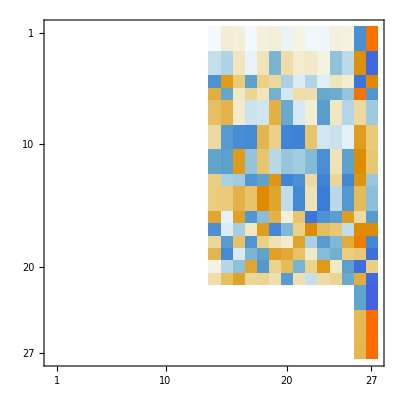

```mathematica
MatrixPlot[vs]
```

```mathematica
M0Big = ArrayFlatten[({{□, □, 0}, {□, □, 0}, {0, 0, ConstantArray[0,{c,c}]}})];
M1Big=ArrayFlatten[({{0, B, Gᵀ}, {B, 0, 0}, {G, 0, 0}})];
{λs,vs} =Sort[Chop[Eigensystem[{M0Big,M1Big}]]ᵀ]ᵀ;
λs
```

{-3.83599,-2.0191+0.224868 ⅈ,-2.0191-0.224868 ⅈ,-1.13095-2.30659 ⅈ,-1.13095+2.30659 ⅈ,-0.418531-0.0842568 ⅈ,-0.418531+0.0842568 ⅈ,-0.323511+0.229454 ⅈ,-0.323511-0.229454 ⅈ,-0.146844+5.33786 ⅈ,-0.146844-5.33786 ⅈ,-0.08791-0.0271893 ⅈ,-0.08791+0.0271893 ⅈ,-0.0665248,-2.37648×10^-8,2.37648×10^-8,0.159302-0.0313006 ⅈ,0.159302+0.0313006 ⅈ,0.204316-0.196461 ⅈ,0.204316+0.196461 ⅈ,0.256525,0.805966,1.29504,1.72635,2.75087,ComplexInfinity,ComplexInfinity}

```mathematica
{y1,y2}=Partition[vs⟦1,1;;2m⟧,m];λ=vs⟦1,2m+1;;-1⟧;
Map[Dimensions,{y1,y2,λ}]
```

{{12},{12},{3}}

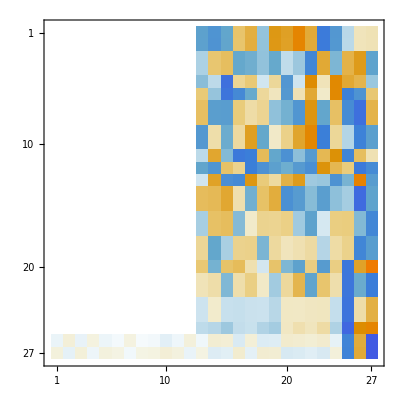

{ComplexInfinity,ComplexInfinity,-0.146844-5.33786 ⅈ,-0.146844+5.33786 ⅈ,-3.83599+0. ⅈ,2.75087+0. ⅈ,-1.13095-2.30659 ⅈ,-1.13095+2.30659 ⅈ,-2.0191+0.224868 ⅈ,-2.0191-0.224868 ⅈ,1.72635+0. ⅈ,1.29504+0. ⅈ,0.805966+0. ⅈ,-0.418531-0.0842568 ⅈ,-0.418531+0.0842568 ⅈ,-0.323511+0.229454 ⅈ,-0.323511-0.229454 ⅈ,0.204316+0.196461 ⅈ,0.204316-0.196461 ⅈ,0.256525+0. ⅈ,0.159302+0.0313006 ⅈ,0.159302-0.0313006 ⅈ,-0.08791-0.0271893 ⅈ,-0.08791+0.0271893 ⅈ,-0.0665248+0. ⅈ,2.3765×10^-8+0. ⅈ,-2.3765×10^-8+0. ⅈ}

```mathematica
MatrixPlot[NewV=Chop[Eigenvectors[{M0Big,M1Big}]]]
vv=NewV⟦-1⟧;
p1=vv⟦1;;m⟧;
Eigenvalues[{M0Big,M1Big}]
```

```mathematica
pMinGEV=-Sign[g.y2] Δ y1/(√(y1.B.y1));
f[p_]:= 0.5 p.A.p + g.p
ECons[p_]:=p.B.p-Δ^2
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
vars=Array[x,m];
vars0=RandomReal[{-1,1},m];
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,vars.B.vars<=Δ^2},{vars, vars0}ᵀ,PrecisionGoal->10] ;
pMinFM=vars/.FMinSub;
TableForm[{{FullForm[f[p]],ECons[p],G.p}/.p->pMinGEV,
{FullForm[f[p]],ECons[p]}/.p->pMinFM},
TableHeadings->{{"GEV","FindMin"},{"obj","cons: p.B.p-Δ^2"}}]
```

| obj | cons: p.B.p-Δ^2 | 
GEV | -0.00377929 | -6.93889×10^-18 | -0.0704259
0.0940681
0.147426
FindMin | -0.281915 | 9.99791×10^-9 |

```mathematica
?Partition
```